```mathematica
Quit[]
```

```mathematica
NN=100;
tmax=10;
h=Partition[Partition[BinaryReadList["hanis_852.dat","Real64"],NN],NN];

film1=ListPlot3D[h⟦10⟧, 
Mesh -> None, Ticks->None,
ColorFunction -> "ThermometerColors",
PlotRange ->{ All,All,{0,2}},
Boxed->False,
Axes->False,
ViewPoint->{1,-8,10}]
```

```mathematica
"Densite d'ilots"

(* POUR CALCULER LA DENSITE D'ILOTS *)

{"th = ",th=0.2}
(* Definition du seuil *)

(* Read data*)
{N2t,hmoy,morhperiodic}=Module[
{name,h,binht,moyh,moy,morht,ah,ph,N2t=0,perx,pery,morhtemp,morhper},
h=Partition[Partition[BinaryReadList["hred-anis.dat","Real64"],NN],NN];
moyh=Table[Mean[Mean[h⟦time⟧]],{time,1,tmax}];
binht=Map[Function[time,Map[If[(#-moyh⟦time⟧)>th,1,0]&,h⟦time⟧,{-1}]],Range[tmax]];
morht=Map[Function[time,MorphologicalComponents[Image[binht⟦time⟧],CornerNeighbors-> False]],Range[tmax]];
Table[Subscript[perx, t]=Select[Table[{morht⟦t⟧⟦1,i⟧,morht⟦t⟧⟦-1,i⟧},{i,n}],#⟦1⟧>0&&#⟦2⟧>0&],{t,tmax}];Table[Subscript[pery, t]=Select[Table[{morht⟦t⟧⟦i,1⟧,morht⟦t⟧⟦i,-1⟧},{i,n}],#⟦1⟧>0&&#⟦2⟧>0&],{t,tmax}];
morhtemp=Map[Function[t,If[Dimensions[Subscript[perx, t]]⟦1⟧>0,ReplaceAll[morht⟦t⟧,Table[Subscript[perx, t]⟦k,2⟧->Subscript[perx, t]⟦k,1⟧,{k,Dimensions[Subscript[perx, t]]⟦1⟧}]],morht⟦t⟧]],Range[tmax]];morhper=Map[Function[t,If[Dimensions[Subscript[pery, t]]⟦1⟧>0,ReplaceAll[morhtemp⟦t⟧,Table[Subscript[pery, t]⟦k,2⟧->Subscript[pery, t]⟦k,1⟧,{k,Dimensions[Subscript[pery, t]]⟦1⟧}]],morhtemp⟦t⟧]],Range[tmax]];
N2t=N2t+Table[Dimensions[Tally[Flatten[morhper⟦t⟧]]]⟦1⟧-1,{t,tmax}];
{N2t,moyh ,morhper}];
```

```mathematica
(* CALCUL DES DISTRIBUTIONS DE VOLUME *)

binh=10;
h=Partition[Partition[BinaryReadList["hred-anis.dat","Real64"],NN],NN];

fmor=Flatten[morhperiodic⟦tmax⟧];

fh=Flatten[h⟦tmax⟧];
(* attention au facteur L/n pour le dx dy*) 
LL=100; 
volilo=Table[Total[Part[fh,Flatten[Position[fmor,numclus]]]](LL/NN)^2,{numclus,Max[Max[morhperiodic⟦tmax⟧]]}]
```

```mathematica
volilot=Flatten[volilo];
{vmoy=Mean[volilot],Δv=StandardDeviation[volilot],nbilot=Dimensions[volilot]⟦1⟧};
Histogram[volilot,{0,40,2},PlotRange->{{0,32},{0,230}}]
Table[{"<v> = ",Subscript[vmoy, num],"Δv = ",Subscript[Δv, num],"nb ilots = ",Subscript[nbilot, num],"Δv / <v> = ",Subscript[Δv, num]/Subscript[vmoy, num],"h_w = ",Subscript[hw, num,1]⟦Subscript[nt, num]⟧},{num,nbsimul}]
```

```mathematica
binv=2;
maxvhisto=30;
maxhisto=130;
stylesize=30;


bc=BinCounts[volilot,binv] ;
histo=Table[{binv*i,bc⟦i⟧},{i,Dimensions[bc]⟦1⟧}];
fighisto=ListLinePlot[histo,Filling->Axis,Mesh->None,PlotRange->{{0,maxvhisto},{0,maxhisto}},InterpolationOrder->0,Frame->True,PlotStyle->{PointSize[0.01],Thickness[0.003],Black},FrameTicks->{{0,5,10,15,20,25},{0,50,100},None,None},
FrameTicksStyle->Directive[22],FrameLabel->{Style["v",stylesize],Style["Counts",stylesize]},FillingStyle->{Directive[Opacity[0.7],Gray]},Epilog->Inset[Style["(a0)",stylesize],{27,110}]]
```

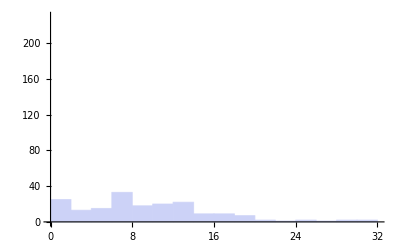
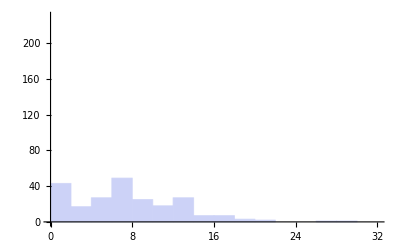
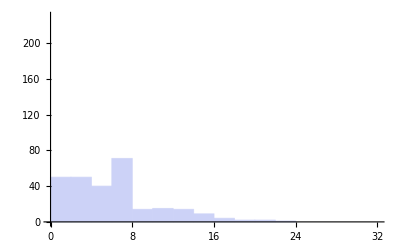
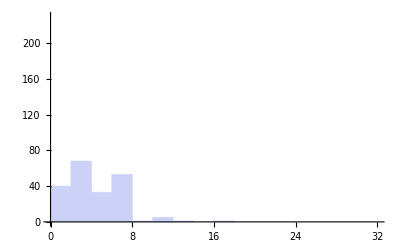
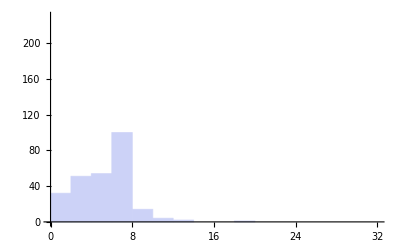
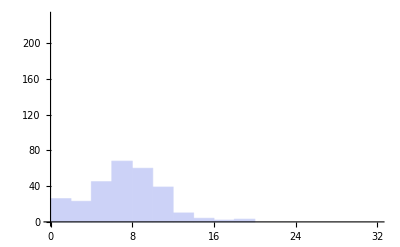
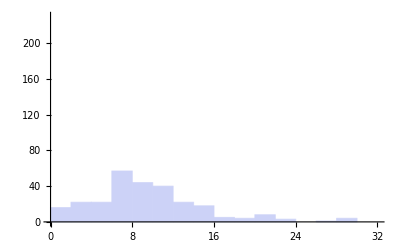

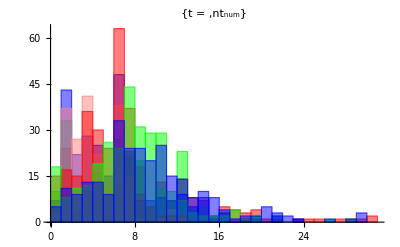

{{<v> = ,9.57916,Δv = ,6.33555,nb ilots = ,181,Δv / <v> = ,0.661389,h_w = ,0.0545794},{<v> = ,7.58846,Δv = ,5.10467,nb ilots = ,227,Δv / <v> = ,0.672688,h_w = ,0.054832},{<v> = ,6.14802,Δv = ,4.31821,nb ilots = ,272,Δv / <v> = ,0.702375,h_w = ,0.0543893},{<v> = ,4.36528,Δv = ,2.47161,nb ilots = ,202,Δv / <v> = ,0.566196,h_w = ,0.0552912},{<v> = ,5.20555,Δv = ,2.55144,nb ilots = ,258,Δv / <v> = ,0.490137,h_w = ,0.0552794},{<v> = ,7.36144,Δv = ,3.54614,nb ilots = ,280,Δv / <v> = ,0.481718,h_w = ,0.0541682},{<v> = ,9.48227,Δv = ,5.40609,nb ilots = ,266,Δv / <v> = ,0.570126,h_w = ,0.0585317}}

```mathematica
volilot=Flatten[Table[Subscript[volilo, num,jeu],{jeu,1,nbjeu⟦num⟧}]],{num,1,nbsimul}];
Table[{Subscript[vmoy, num]=Mean[Subscript[volilot, num]],Subscript[Δv, num]=StandardDeviation[Subscript[volilot, num]],Subscript[nbilot, num]=Dimensions[Subscript[volilot, num]]⟦1⟧},{num,1,nbsimul}];
Table[Histogram[Subscript[volilot, num],{0,40,2},PlotRange->{{0,32},{0,230}}],{num,nbsimul}]
Histogram[Table[Subscript[volilot, num],{num,1,nbsimul}],PlotLabel->{"t = ",Subscript[nt, num]},PlotRange->All,ChartStyle->{Red,Green,Blue,Pink}]
Table[{"<v> = ",Subscript[vmoy, num],"Δv = ",Subscript[Δv, num],"nb ilots = ",Subscript[nbilot, num],"Δv / <v> = ",Subscript[Δv, num]/Subscript[vmoy, num],"h_w = ",Subscript[hw, num,1]⟦Subscript[nt, num]⟧},{num,nbsimul}]
```

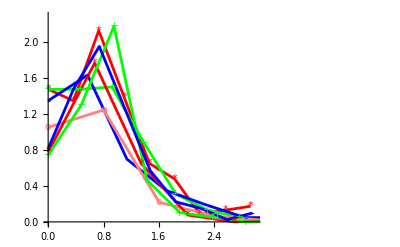

integrale de la fonction de rescaling

```mathematica
htot=Last[hmoy⟦1⟧];
vmax=33;
binv=3.5;
simulrescalmin=1;
simulrescalmax=7;

bc=BinCounts[volilot,{0,vmax,binv}];
histo=Table[{binv*i/vmoy,bc⟦i+1⟧},{i,0,vmax/binv-1}];
histor=Table[{binv*i/vmoy,bc⟦i+1⟧vmoy^2/(htot)/NN^2},{i,0,vmax/binv-1}];

ListPlot[histor,Filling->Axis,Joined->True,Mesh->All,PlotRange->{{0,3},{0,120}}]

maxi=Max[Max[Table[histo⟦i,2⟧,{i,Dimensions[histo]⟦1⟧}]]];
maxir=Max[Max[Table[histor⟦i,2⟧,{i,Dimensions[histor]⟦1⟧}]]];


ListPlot[histor],Joined->True,Mesh->All,PlotStyle->{{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Blue,Thickness[0.005]},{Pink,Thickness[0.005]}} ,PlotMarkers-> {{"*",Large},{"+",Large},{"-",Large},{"o",Large}},PlotRange->{{0,3},{0,1.05maxir}}]
" fonction de rescaling "
```